```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
```

# Integration

Theory

## ToDo

Deﬁnition II.1.1 A curve
Deﬁnition II.1.2 A smooth curve
Deﬁnition II.1.3 A piecewise smooth curve
Deﬁnition II.1.4 A line integral or contour integral
Definition Arc Length
Remark II.1.5 Complex line integral properties
  Linearity
  Standard estimate
  Generalizes ordinary Riemann integral
  Parameter invariance
  Main theorem of calculus
Theorem II.1.6 ( If f has primitive on D then closed contour integral is 0 )
Remark II.1.7 ( 1/z -> 2 pi I )
Corollary II.1.7_1 ( 1/z has no primitive )

## Examples

```mathematica
f[z_]:=z^2/(z-4-3ⅈ)
Subscript[a, 1][t_]:=(1+ⅈ)t
Subscript[a, 2][t_]:=ⅈ t^2+t

Subscript[a, 1][t_]:=4+3 I+ⅇ^(2π I t)
f[3.5+3I]
```

-6.5-42. ⅈ

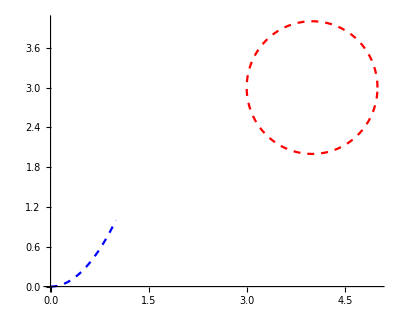

(-48+14 ⅈ) π

(1+8 ⅈ)+(7/2+12 ⅈ) Log[323/625-(36 ⅈ)/625]

```mathematica
g1=ParametricPlot[ReIm[Subscript[a, 1][t]],{t,0,1},PlotStyle->{Red,Dashed}];
g2=ParametricPlot[ReIm[Subscript[a, 2][t]],{t,0,1},PlotStyle->{Blue,Dashed}];
Show[Graphics @@ g1,g2,PlotRange->All,AxesOrigin->{0,0}]
Integrate[f[Subscript[a, 1][t]]Subscript[a, 1]'[t],{t,0,1}]
Integrate[f[Subscript[a, 2][t]]Subscript[a, 2]'[t],{t,0,1}]
```

Exercises

## Exercises II.1

### FrBu II.1 - 2

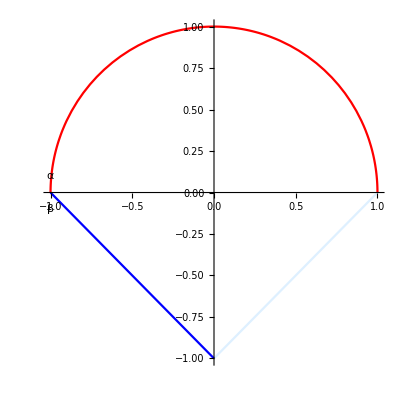

```mathematica
g1=ParametricPlot[ReIm[Exp[I θ]],{θ,0,Pi},PlotStyle->{Red}];
g2=ParametricPlot[ReIm[1+t(-I-1)],{t,0,1},PlotStyle->{LightBlue}];
g3=ParametricPlot[ReIm[1-t+I(t-2)],{t,1,2},PlotStyle->{Blue}];
Show[Graphics@@g1,g2,g3,PlotRange->All,
Epilog->{Text["α",{-1,0.1}],Text["β",{-1,-0.1}]}]
```

```mathematica
Integrate[1/ⅇ^(ⅈ t)ⅈ ⅇ^(ⅈ t),{t,0,π}]
```

ⅈ π

```mathematica
Integrate[1/(1+t(-I-1))(-I-1),{t,0,1}]+Integrate[1/(1-2I+t(-1+I))(I-1),{t,1,2}]
```

-ⅈ π

```mathematica
Integrate[1/(1+t(-I-1))(-I-1),t]
```

Log[-1+(1+ⅈ) t]

```mathematica
Log[I]-Log[-1]
```

-(ⅈ π)/2

```mathematica
Integrate[1/(1-2I+t(-1+I))(I-1),t]
```

Log[(-2-ⅈ)+(1+ⅈ) t]

```mathematica
Log[I]-Log[-1]
```

-(ⅈ π)/2

### FrBu II.1 - 4

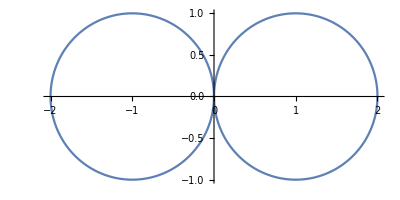

```mathematica
g1=ParametricPlot[ReIm[1-ⅇ^(ⅈ t)],{t,0,2π}];
g2=ParametricPlot[ReIm[-1-ⅇ^(ⅈ t)],{t,2π,4π}];
Show[Graphics@@g1,g2,PlotRange->All]
```

### FrBu II.1 - 5

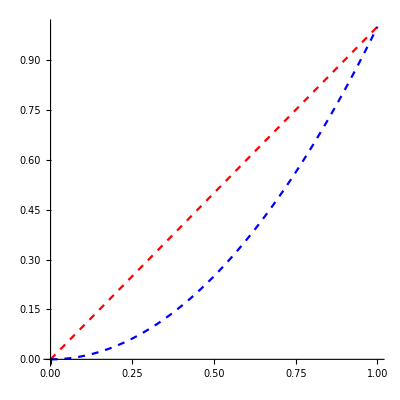

1/2 (-1+ⅇ^(2 ⅈ))

1/2 (-1+ⅇ^(2 ⅈ))

```mathematica
f[z_]:=z ⅇ^(z^2)
Subscript[a, 1][t_]:=(1+ⅈ)t
Subscript[a, 2][t_]:=ⅈ t^2+t
g1=ParametricPlot[ReIm[Subscript[a, 1][t]],{t,0,1},PlotStyle->{Red,Dashed}];
g2=ParametricPlot[ReIm[Subscript[a, 2][t]],{t,0,1},PlotStyle->{Blue,Dashed}];
Show[Graphics @@ g1,g2,PlotRange->All,AxesOrigin->{0,0}]
Integrate[f[Subscript[a, 1][t]]Subscript[a, 1]'[t],{t,0,1}]
Integrate[f[Subscript[a, 2][t]]Subscript[a, 2]'[t],{t,0,1}]
```

### FrBu II.1 - 6

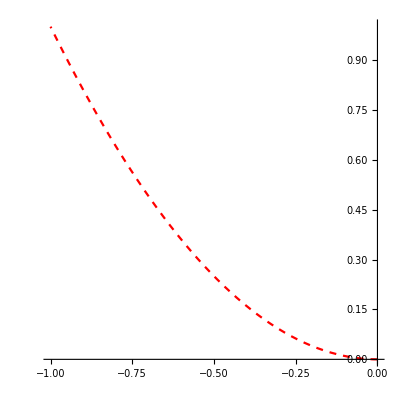

1-Cosh[1+ⅈ]

```mathematica
ClearAll[f];
f[z_]:=Sin[z]
Subscript[a, 1][t_]:=-t+t^2 ⅈ
g1=ParametricPlot[ReIm[Subscript[a, 1][t]],{t,0,1},PlotStyle->{Red,Dashed}];
Show[Graphics @@ g1,PlotRange->All,AxesOrigin->{0,0}]
Integrate[f[Subscript[a, 1][t]]Subscript[a, 1]'[t],{t,0,1}]
```

```mathematica
Integrate[Sin[-t+t^2 ⅈ](-1+2t ⅈ),t]
```

-Cos[(1-ⅈ t) t]

```mathematica
t1[t_]:=-Cos[(-1+ⅈ t) t]
```

```mathematica
t1[1]-t1[0]
```

1-Cosh[1+ⅈ]

### FrBu II.1 - 7

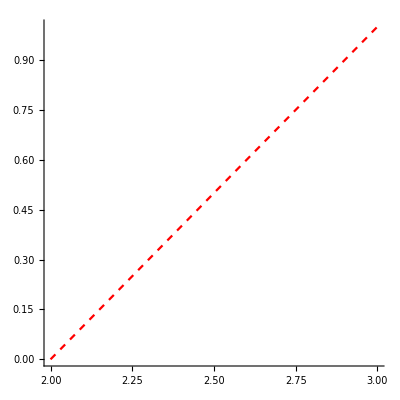

10/3+(26 ⅈ)/3

```mathematica
ClearAll[f,a];
f[z_]:=z^2
a[t_]:=(1-ⅈ)+t(1+ⅈ)
g1=ParametricPlot[ReIm[a[t]],{t,1,2},PlotStyle->{Red,Dashed}];
Show[Graphics @@ g1,PlotRange->All,AxesOrigin->{0,0}]
Integrate[f[a[t]]a'[t],{t,1,2}]
```

### FrBu II.1 - 8

```mathematica
ClearAll[f,a];
f[z_]:=ⅇ^(ⅈ z^2)
a[t_]:=ⅇ^(ⅈ t)
a[t_]:=Abs[-ⅈ Sin[2t]]
Abs[Integrate[f[a[t]]a'[t],{t,0,π/4}]]//N
Integrate[Abs[f[a[t]]a'[t]],{t,0,π/4}]//N
π/4//N
```

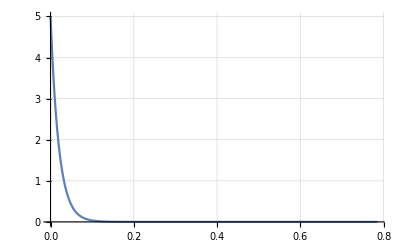

```mathematica
Plot[Abs[f[a[t]]a'[t]],{t,0,π/4},AxesOrigin->{0,0},PlotRange->Full, GridLines->Automatic]
```

```mathematica
(π(1-ⅇ^-1))/4//N
```

0.496466

## Exercises II.2

### FrBu II.2 - 1

#### FrBu II.2 - 1a

```mathematica
ClearAll[f,x,y]
f[z_]:=Abs[z^2-3]
```

```mathematica
ComplexExpand[Abs[(x+I y)^2-3]]
```

√(4 x^2 y^2+(-3+x^2-y^2)^2)

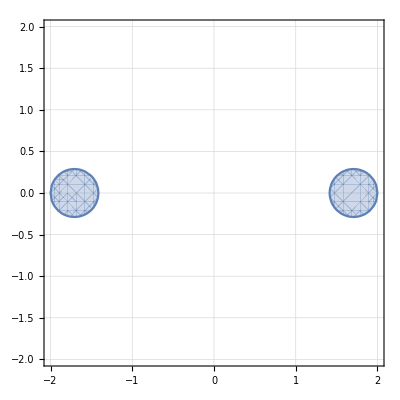

```mathematica
RegionPlot[√(4 x^2 y^2+(-3+x^2-y^2)^2)<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

```mathematica
RegionPlot[4 x^2 y^2+(-3+x^2-y^2)^2<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
Expand[4 x^2 y^2+(-3+x^2-y^2)^2]
```

9-6 x^2+x^4+6 y^2+2 x^2 y^2+y^4

```mathematica
RegionPlot[9-6 x^2+x^4+6 y^2+2 x^2 y^2+y^4<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

#### FrBu II.2 - 1b

```mathematica
ClearAll[f,x,y]
f[z_]:=Abs[z^2-1]
```

```mathematica
ComplexExpand[Abs[(x+I y)^2-1]]
```

√(4 x^2 y^2+(-1+x^2-y^2)^2)

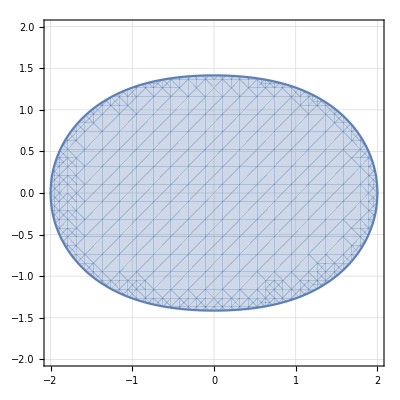

```mathematica
RegionPlot[√(4 x^2 y^2+(-1+x^2-y^2)^2)<3,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

```mathematica
RegionPlot[4 x^2 y^2+(-1+x^2-y^2)^2<9,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
Expand[4 x^2 y^2+(-1+x^2-y^2)^2]
```

1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4

```mathematica
RegionPlot[1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4<9,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
f[-√2 I]
```

3

```mathematica
Abs[(-1-I)^2-1]//N
```

2.23607

#### FrBu II.2 - 1c

```mathematica
ClearAll[f,x,y]
f[z_]:=Abs[Abs[z^2]-2]
```

```mathematica
ComplexExpand[Abs[Abs[(x+I y)^2]-2]]
```

√((-2+x^2+y^2)^2)

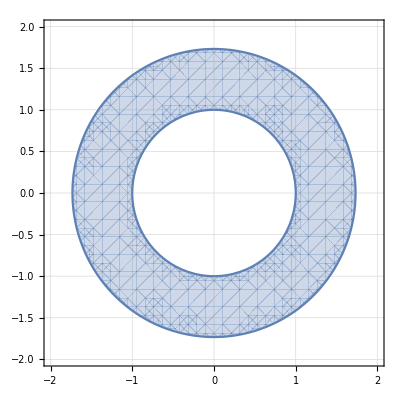

```mathematica
RegionPlot[√((-2+x^2+y^2)^2)<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

```mathematica
RegionPlot[(-2+x^2+y^2)^2<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
Expand[(-2+x^2+y^2)^2]
```

4-4 x^2+x^4-4 y^2+2 x^2 y^2+y^4

```mathematica
RegionPlot[4-4 x^2+x^4-4 y^2+2 x^2 y^2+y^4<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
√3.
```

1.73205

```mathematica
f[-I 1.7320508075688772]
```

1.

#### FrBu II.2 - 1d

```mathematica
ClearAll[f,x,y]
f[z_]:=Abs[z^2-1]
```

```mathematica
ComplexExpand[Abs[(x+I y)^2-1]]
```

√(4 x^2 y^2+(-1+x^2-y^2)^2)

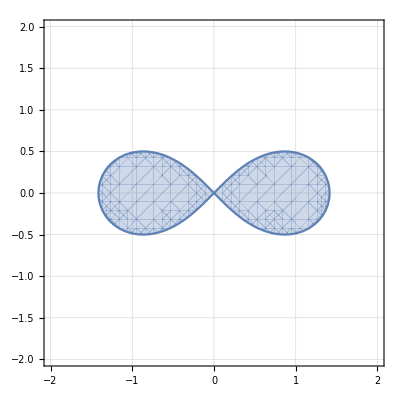

```mathematica
RegionPlot[√(4 x^2 y^2+(-1+x^2-y^2)^2)<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

```mathematica
RegionPlot[4 x^2 y^2+(-1+x^2-y^2)^2<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
Expand[4 x^2 y^2+(-1+x^2-y^2)^2]
```

1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4

```mathematica
RegionPlot[1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

#### FrBu II.2 - 1e

```mathematica
ClearAll[f,x,y]
f[z_]:=z+Abs[z]
```

```mathematica
ComplexExpand[ReIm[x+I y+Abs[(x+I y)]]]
```

{x+√(x^2+y^2),y}

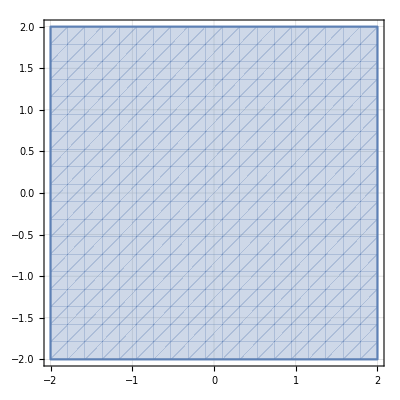

```mathematica
RegionPlot[x+√(x^2+y^2)-y≠0,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

### FrBu II.2 - 5

#### FrBu II.2 - 5a

```mathematica
ClearAll[f,a];
f[z_]:=1/Abs[z]
a[t_]:=ⅇ^(2π I t)
Integrate[f[a[t]]a'[t],{t,0,1}]
```

0

```mathematica
Integrate[1/Abs[z],z]
Simplify[1/a[t],Element[t,Reals]]
Simplify[Abs[1/a[t]],Element[t,Reals]]
```

∫1/Abs[z]ⅆz

ⅇ^(-2 ⅈ π t)

```mathematica
ⅇ^(-2 ⅈ π t)//tex
```

e^{-2 i \pi  t}

```mathematica
Simplify[f[a[t]],Element[t,Reals]]
a[t]
a'[t]
Simplify[a'[t],Element[t,Reals]]
Simplify[f[a[t]]a'[t],Element[t,Reals]]
```

1

ⅇ^(2 ⅈ π t)

2 ⅈ ⅇ^(2 ⅈ π t) π

2 ⅈ ⅇ^(2 ⅈ π t) π

2 ⅈ ⅇ^(2 ⅈ π t) π

```mathematica
2 ⅈ ⅇ^(2 ⅈ π t) π//tex
```

2 i e^{2 i \pi  t} \pi

```mathematica
ⅇ^(2 ⅈ π 1)-ⅇ^(2 ⅈ π 0)
```

0

#### FrBu II.2 - 5b

```mathematica
ClearAll[f,a];
f[z_]:=1/Abs[z]^2
a[t_]:=ⅇ^(2π I t)
Integrate[f[a[t]]a'[t],{t,0,1}]
```

0

```mathematica
Integrate[1/Abs[z]^2,z]
Simplify[1/a[t],Element[t,Reals]]
Simplify[1/Abs[a[t]]^2,Element[t,Reals]]
```

∫1/Abs[z]^2 ⅆz

ⅇ^(-2 ⅈ π t)

1

```mathematica
Simplify[f[a[t]],Element[t,Reals]]
a[t]
a'[t]
Simplify[a'[t],Element[t,Reals]]
Simplify[f[a[t]]a'[t],Element[t,Reals]]
```

1

ⅇ^(2 ⅈ π t)

2 ⅈ ⅇ^(2 ⅈ π t) π

2 ⅈ ⅇ^(2 ⅈ π t) π

2 ⅈ ⅇ^(2 ⅈ π t) π

```mathematica
ⅇ^(2 ⅈ π 1)-ⅇ^(2 ⅈ π 0)
```

0

#### FrBu II.2 - 5c

```mathematica
ClearAll[f,g,a];
f[z_]:=1/3 1/(4/3+z)
g[z_]:=Abs[f[z]]
a[t_]:=ⅇ^(2π I t)
Integrate[f[a[t]]a'[t],{t,0,1}]
Integrate[Abs[a'[t]],{t,0,1}]
{g[1],g[I],g[-1],g[-I]}//N
```

0

2 π

{0.142857,0.2,1.,0.2}

```mathematica
Integrate[1/(4+3z),z]
Simplify[f[a[t]]a'[t],Element[t,Reals]]
```

1/3 Log[4+3 z]

(2 ⅈ ⅇ^(2 ⅈ π t) π)/(4+3 ⅇ^(2 ⅈ π t))

```mathematica
(2 ⅈ ⅇ^(2 ⅈ π 1) π)/(4+3 ⅇ^(2 ⅈ π 1))-(2 ⅈ ⅇ^(2 ⅈ π 0) π)/(4+3 ⅇ^(2 ⅈ π 0))
```

0

## Exercises II.3

### FrBu II.3 - 1

#### FrBu II.3 - 1a

```mathematica
ClearAll[f,a];
f[z_]:=z^7/(z^2(z^4+1))
a[t_]:=2+ⅇ^(I t)
Integrate[f[a[t]]a'[t],{t,0,2π}]
```

0

#### FrBu II.3 - 1b

```mathematica
ClearAll[f,a];
f[z_]:=z^7/(z^2(z^4+1))
g[z_]:=z^7/(z^2(z^4+1))
a[t_]:=1+3/2 ⅇ^(I t)
Integrate[f[a[t]]a'[t],{t,0,2π}]
```

0

#### FrBu II.3 - 1c

#### FrBu II.3 - 1d

#### FrBu II.3 - 1e

## Temp

### Temp-1

```mathematica
Integrate[(1+I)+t(1+I),{t,1,2}]
```

5/2+(5 ⅈ)/2

```mathematica
Integrate[((1+I)+(t/4-11/8)(1+I)),{t,2,6}]
```

5/2+(5 ⅈ)/2

```mathematica
60/2*5
```

150

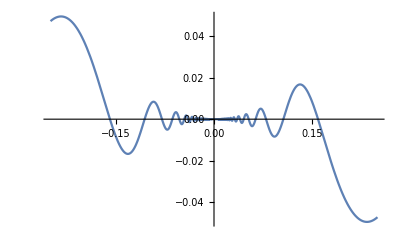

```mathematica
ClearAll[f];
f[x_]:=x^2 Sin[1/x]
Plot[f[x],{x,-0.25,0.25}]
```

```mathematica
ClearAll[f];
f[z_]:=Sum[(-1)^(n+1)1/n z^n,{n,1,Infinity}]
Table[(-1)^(n+1)1/n z^n,{n,1,6}]
f[0.75]
Log[1+0.75]
Series[Log[1+z],{z,1,6}]
```

{z,-z^2/2,z^3/3,-z^4/4,z^5/5,-z^6/6}

0.559616

0.559616

Log[2]+(z-1)/2-1/8 (z-1)^2+1/24 (z-1)^3-1/64 (z-1)^4+1/160 (z-1)^5-1/384 (z-1)^6+O[z-1]^7

```mathematica
1/ⅇ^(1/2 π)//N
```

0.20788

### Temp-2

```mathematica
1/(√π)Integrate[ⅇ^(-x^2),{x,-Infinity,Infinity}]//tex
```

\frac{\int_{-\infty }^{\infty } e^{-x^2} \, dx}{\sqrt{\pi }}

```mathematica
ClearAll[f,a];
f[z_]:=(z+1)/(z-2)^2
f[z_]:=1
a[t_]:=1+2 ⅇ^(I t)
a[t_]:=Cos[t]^7+I Sin[t]^7
NIntegrate[Abs[a'[t]],{t,0,2/4 1π}]
```

1.85842

```mathematica
%//N
```

1.72522

```mathematica
Integrate[(x^2 Cos[x]+2 x Sin[x])ⅇ^(x^2 Sin[x]),x]
```

ⅇ^(x^2 Sin[x])

```mathematica
D[x^2 Sin[x],x]
```

x^2 Cos[x]+2 x Sin[x]

```mathematica
π^12//N
```

924269.

```mathematica
Manipulate[
g1=ParametricPlot[ReIm[Cos[2π t]^a+I Sin[2π t]^a],{t,0,1},PlotStyle->{Blue}];
Show[Graphics@@g1,PlotRange->All],
{a,1,17,2}]
```

### Temp-3 ( Cauchy IT Triangle Paths - Ivan Francis Wilde

```mathematica
ClearAll[f,a];
f[z_]:=2 z^3
a=I;
τ[z_]:=Piecewise[{{(f[z]-f[a])/(z-a)-f'[a],z!=a},{0,z==a}}]
g[z_]:=f[a]+(z-a)f'[a]+(z-a)τ[z]
ComplexPlot3D[τ[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
f[-1]
g[-1]
τ[I]
```

-Graphics3D-

-2

-2

0

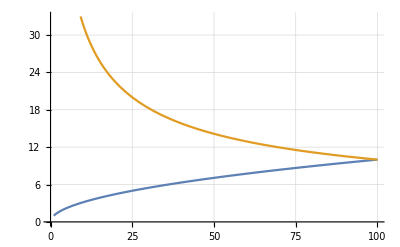

```mathematica
Plot[{√x,100(√x)/x},{x,1,100},AxesOrigin->{0,0},GridLines->Automatic]
```

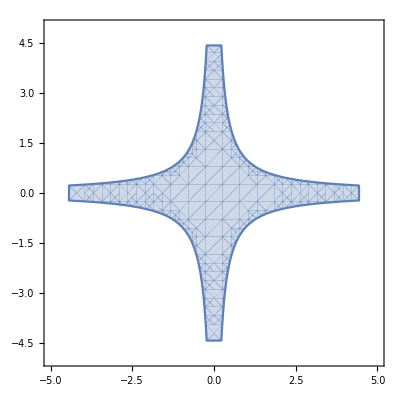

```mathematica
RegionPlot[Abs[x y]<1&&-5<x&&x<5&&-5<y&&y<5,{x,-5,5},{y,-5,5}]
```

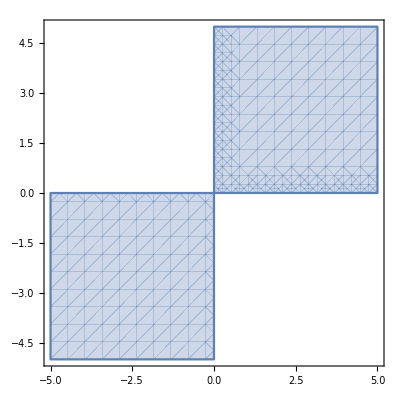

```mathematica
RegionPlot[x y>0&&-5<x&&x<5&&-5<y&&y<5,{x,-5,5},{y,-5,5}]
```

```mathematica
Table[{k,Floor[k+√k+1/2]},{k,1,20}]//TableForm
```

1 | 2
2 | 3
3 | 5
4 | 6
5 | 7
6 | 8
7 | 10
8 | 11
9 | 12
10 | 13
11 | 14
12 | 15
13 | 17
14 | 18
15 | 19
16 | 20
17 | 21
18 | 22
19 | 23
20 | 24

```mathematica
((3+2I)Conjugate[3+2I])^2
```

169

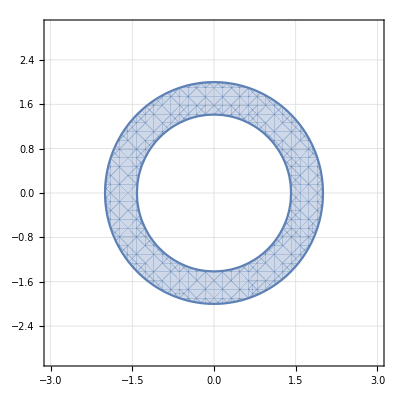

```mathematica
RegionPlot[(x^2+y^2)^2-6(x^2+y^2)+9<1,{x,-3,3},{y,-3,3},GridLines->Automatic]
```

### Temp-4

```mathematica
ClearAll[f,x,y]
f[z_]:=Abs[z^2-3]
```

```mathematica
ComplexExpand[Abs[(x+I y)^2-3]]
```

√(4 x^2 y^2+(-3+x^2-y^2)^2)

```mathematica
RegionPlot[√(4 x^2 y^2+(-3+x^2-y^2)^2)<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
RegionPlot[4 x^2 y^2+(-3+x^2-y^2)^2<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

```mathematica
Expand[4 x^2 y^2+(-3+x^2-y^2)^2]
```

9-6 x^2+x^4+6 y^2+2 x^2 y^2+y^4

```mathematica
RegionPlot[9-6 x^2+x^4+6 y^2+2 x^2 y^2+y^4<1,{x,-2,2},{y,-2,2},GridLines->Automatic]
```

-Graphics-

### Temp-5

```mathematica
ClearAll[a,f];
a[t_]:=5+R ⅇ^(2π ⅈ t)
Integrate[Abs[a'[t]],{t,0,1},Assumptions->{R >0}]
```

2 π R

### Temp-6

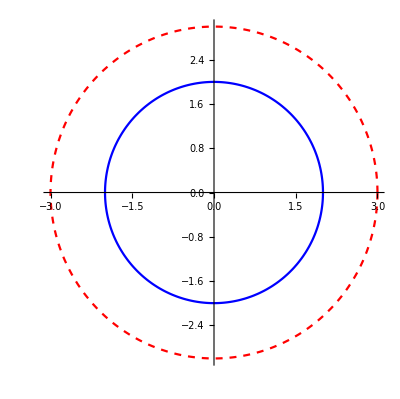

2 ⅈ π

2 ⅈ π

```mathematica
ClearAll[a,b,f];
ClearAll[f];
f[z_]:=1/z
a=3;
b=2;
Subscript[a, 1][t_]:=a Cos[2π t]+ⅈ a Sin[2π t]
Subscript[b, 1][t_]:=b Cos[2π t]+ⅈ b Sin[2π t]
g1=ParametricPlot[ReIm[Subscript[a, 1][t]],{t,0,1},PlotStyle->{Red,Dashed}];
g2=ParametricPlot[ReIm[Subscript[b, 1][t]],{t,0,1},PlotStyle->{Blue}];
Show[Graphics @@ g1,g2,PlotRange->All,AxesOrigin->{0,0}]
Integrate[f[Subscript[a, 1][t]]Subscript[a, 1]'[t],{t,0,1}]
Integrate[f[Subscript[b, 1][t]]Subscript[b, 1]'[t],{t,0,1}]
```

```mathematica
Subscript[a, 1][t]Subscript[b, 1][t]//Expand
```

6 Cos[2 π t]^2+12 ⅈ Cos[2 π t] Sin[2 π t]-6 Sin[2 π t]^2

```mathematica
ClearAll[a,b];
1/(a^2 Cos[t]+b^2 Sin[t])//TrigToExp
```

1/(1/2 ⅈ b^2 (ⅇ^(-ⅈ t)-ⅇ^(ⅈ t))+1/2 a^2 (ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)))

```mathematica
Cosh[I t]//TrigToExp
```

ⅇ^(-ⅈ t)/2+ⅇ^(ⅈ t)/2

```mathematica
Integrate[1/((a Cos[t])^2+(b Sin[t])^2),{t,0,2π},Assumptions->{a ϵ Reals, b ϵ Reals}]
```

(2 ⅈ (Log[-(ⅈ b)/a]-Log[(ⅈ b)/a]))/(a b)

```mathematica
(2 ⅈ (Log[-(ⅈ 3)/2]-Log[(ⅈ 3)/2]))/6
```

π/3

```mathematica
Log[-(ⅈ 3)/2]//N
Log[(ⅈ 3)/2]//N
```

0.405465-1.5708 ⅈ

0.405465+1.5708 ⅈ

```mathematica
Cos[π/2]
Cos'[π/2]
Cos''[π/2]
```

0

-1

0

```mathematica
ClearAll[f,g]
f[z_]:=(z-2)^3(z^2+1)(z-ⅈ)ⅇ^z
Reduce[f[z]==0,z]
g[z_]:=(z^2+1)
D[f[z],{z,0}]
D[f[z],{z,1}]
```

z==-ⅈ||z==ⅈ||z==2

ⅇ^z (-2+z)^3 (-ⅈ+z) (1+z^2)

2 ⅇ^z (-2+z)^3 z (-ⅈ+z)+ⅇ^z (-2+z)^3 (1+z^2)+3 ⅇ^z (-2+z)^2 (-ⅈ+z) (1+z^2)+ⅇ^z (-2+z)^3 (-ⅈ+z) (1+z^2)

```mathematica
h[z_]:=2 ⅇ^z (-2+z)^3 z (-ⅈ+z)+ⅇ^z (-2+z)^3 (1+z^2)+3 ⅇ^z (-2+z)^2 (-ⅈ+z) (1+z^2)+ⅇ^z (-2+z)^3 (-ⅈ+z) (1+z^2)
```

```mathematica
f'[I]
```

0

```mathematica
Series[(z^3+1)/(z(z^2+1)),{z,0,9}]
```

1/z-z+z^2+z^3-z^4-z^5+z^6+z^7-z^8-z^9+O[z]^10

```mathematica
Series[(z^3+1)/(z^2+1),{z,0,9}]
```

1-z^2+z^3+z^4-z^5-z^6+z^7+z^8-z^9+O[z]^10

```mathematica
Series[Sin[z]/z^3,{z,0,9}]
```

1/z^2-1/6+z^2/120-z^4/5040+z^6/362880-z^8/39916800+O[z]^10

```mathematica
1440 365//N
```

525600.

```mathematica
ClearAll[f];
f[z_]:=(z+I)/(z^2+1)
g[z_]:=1/(z-I)
Limit[f[z],z->-I]
```

ⅈ/2

```mathematica
Table[{f[k],g[k]},{k,3,7}]//TableForm
```

3/10+ⅈ/10 | 3/10+ⅈ/10
4/17+ⅈ/17 | 4/17+ⅈ/17
5/26+ⅈ/26 | 5/26+ⅈ/26
6/37+ⅈ/37 | 6/37+ⅈ/37
7/50+ⅈ/50 | 7/50+ⅈ/50

```mathematica
Series[(3 z)/Tan[z],{z,0,6}]
```

3-z^2-z^4/15-(2 z^6)/315+O[z]^7

```mathematica
Series[(3z)/Tan[z],{z,0,6}]
```

3-z^2-z^4/15-(2 z^6)/315+O[z]^7

```mathematica
Tan[0]
```

0

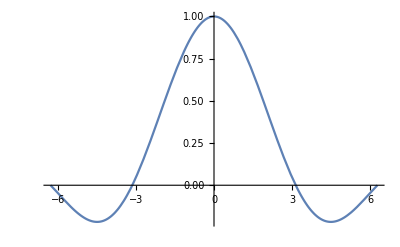

```mathematica
Plot[Sin[x]/x,{x,-2π,2π}]
```

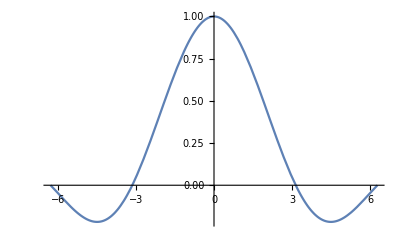

```mathematica
Plot[Sinc[x],{x,-2π,2π}]
```